## Tahm — PS 10 — 2025-02-25

## EIWL3 Sections 26, 27, and 28

# Chapter 26

```mathematica
#^2&/@Range[10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Blend[{Red,#}]&/@{Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
Framed[Column[{ToUpperCase[#],#}]]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}






France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
Grid[{#,EntityValue[#,"Flag"]}&/@EntityList[EntityClass["Country","GroupOf5"]],Frame->Automatic]
```

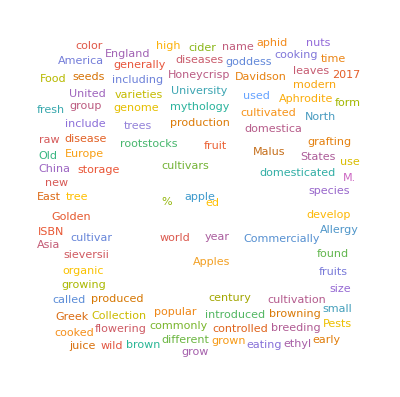
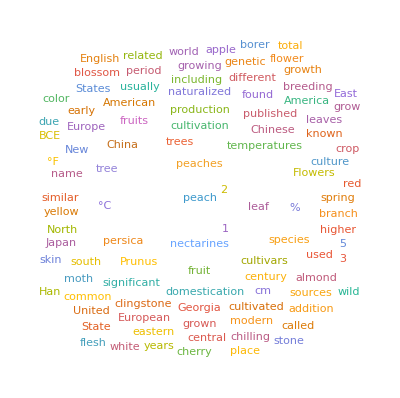
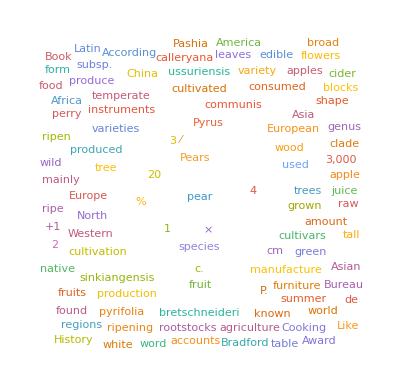

```mathematica
WordCloud[WikipediaData[#]]&/@{"apple","peach", "pear"}
```

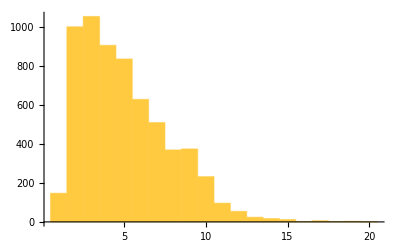
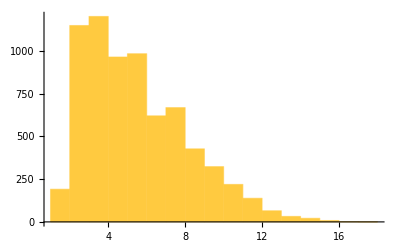
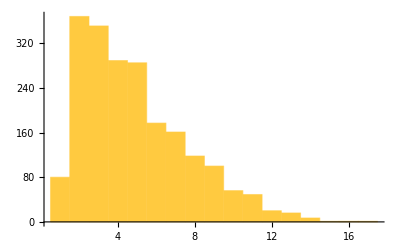

```mathematica
Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach", "pear"}
```

```mathematica
GeoListPlot[{#},GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

# Chapter 27

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
NestList[Rotate[Framed[#],RandomReal[{0,360}]]&,Style["A",50],5]
```

{A,A,A,A,A,A}

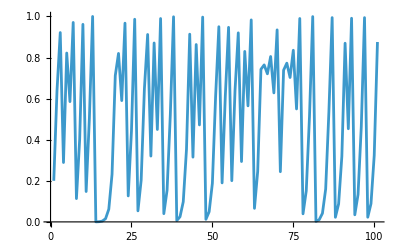

```mathematica
ListLinePlot[NestList[4#(1-#)&,0.2,100]]
```

```mathematica
Nest[1.0+1.0/#&,1,30]//N
```

1.61803

```mathematica
NestList[3*3#&,1,10]
```

{1,9,81,729,6561,59049,531441,4782969,43046721,387420489,3486784401}

```mathematica
NestList[(#+2/#)/2&,1.0,5]-Sqrt[2]
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

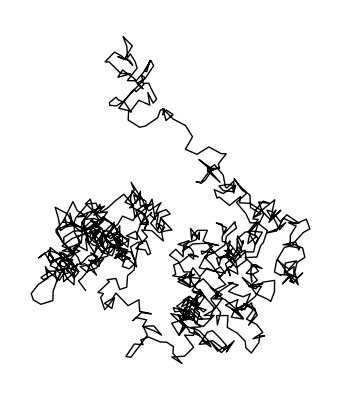

```mathematica
Graphics[Line[NestList[#+RandomReal[{-1,1},2]&,{0,0},1000]]]
```

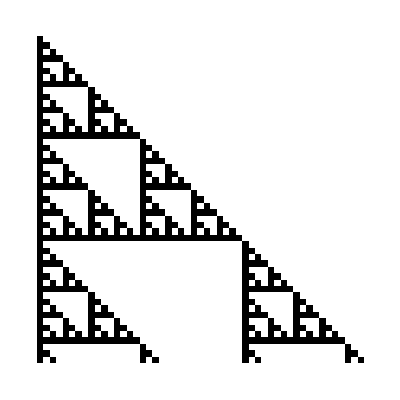

```mathematica
ArrayPlot[
NestList[
Mod[
Join[{0},#]+Join[#,{0}],2]&,
{1},50]]
```

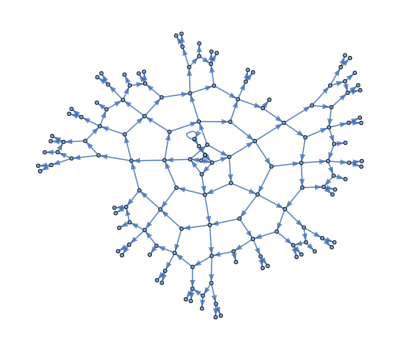

```mathematica
NestGraph[{#+1,2#}&,0,10]
```

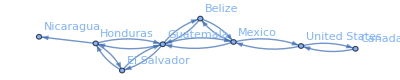

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->All]
```

# Chapter 28

```mathematica
123^321>456^123
```

True

```mathematica
Select[Range[100], Total[IntegerDigits[#]]<5&]
```

{1,2,3,4,10,11,12,13,20,21,22,30,31,40,100}

```mathematica
If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Select[WordList[],StringTake[#,1]==StringTake[StringReverse[#],1]=="p"&]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,peep,penmanship,pep,pickup,pileup,pip,plop,plump,polyp,pomp,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

```mathematica
Select[Array[Prime,100],Last[IntegerDigits[#]]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
Select[RomanNumeral[Range[100]],!MemberQ[Characters[#],"I"]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
Select[RomanNumeral[Range[1000]],StringReverse[#]==#&]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
Select[IntegerName[Range[100]],StringTake[#,1]==StringTake[StringReverse[#],1]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
Select[TextWords[WikipediaData["Words"]],StringLength[#]>15&]
```

{yibi-jarran-gabun,yibi-gabun-jarran,orthographically,multiple-morpheme,Proto-Indo-European,978-0-08-044854-1}

```mathematica
NestList[
If[
EvenQ[#],
#/2,
3#+1]&,
1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

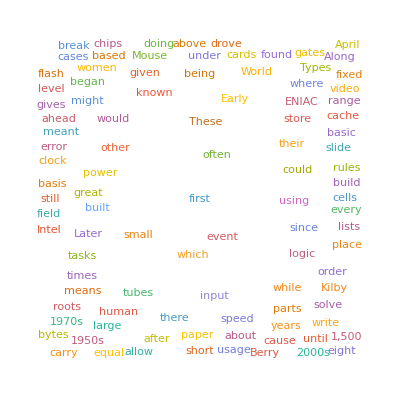

```mathematica
WordCloud[Select[TextWords[WikipediaData["Computers"]],StringLength[#]==5&]]
```

```mathematica
Select[WordList[],StringLength[#]>=3&&#!=StringReverse[#]&&StringTake[#,3]==StringTake[StringReverse[#],3]&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
Select[Select[WordList[],StringLength[#]==10&],Total[LetterNumber/@Characters[#]]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}

```mathematica
Select[WordList[],StringLength[#]==10&]
```

{abbreviate,abdication,aberration,abhorrence,abjuration,abnegation,abnormally,abominable,abominably,aboriginal,abortively,aboveboard,abridgment,abrogation,abruptness,abscission,absolutely,absolution,absolutism,absolutist,absorbency,absorption,absorptive,abstemious,abstention,abstinence,abstracted,abstracter,abstractly,abstrusely,abundantly,accelerate,accentuate,acceptable,acceptably,acceptance,accessible,accidental,accomplice,accomplish,accordance,accountant,accounting,accoutered,accredited,accumulate,accurately,accusation,accusative,accusatory,accusingly,accustomed,achievable,achromatic,acoustical,acquainted,acquirable,acrobatics,acrophobia,actionable,activating,activation,activeness,adaptation,additional,adequately,adjectival,adjudicate,adjuration,adjustable,adjustment,administer,admiration,admiringly,admissible,admittance,admittedly,admonition,admonitory,adolescent,adrenaline,adroitness,adsorption,adulterant,adulterate,adulterous,adventurer,advertised,advertiser,advisement,aerobatics,aeronautic,aesthetics,affability,affectedly,affiliated,affliction,affordable,aficionado,afterbirth,afterimage,aftershock,aftertaste,aggrandize,aggravated,aggregated,aggression,aggressive,agronomist,airfreight,alarmingly,albuminous,alchemical,alcoholism,algebraist,alienating,alienation,alimentary,alkalinity,allegation,allegiance,allegretto,allergenic,alleviated,alliterate,allocation,allotropic,allurement,alphabetic,altarpiece,alteration,alternator,altogether,altruistic,amalgamate,amanuensis,amateurish,amateurism,ambassador,ambivalent,ambulation,ambulatory,ameliorate,amercement,amiability,ammunition,amphibious,amputation,analogical,analytical,analyzable,anamorphic,anarchical,anatomical,ancestress,androgenic,anemometer,anesthesia,anesthetic,angiosperm,anglophile,angularity,animadvert,animalcule,animatedly,anisotropy,annexation,annihilate,annotating,annotation,annoyingly,anointment,answerable,antagonism,antagonist,antagonize,antebellum,antecedent,anthracite,anthropoid,antibiotic,anticancer,anticipate,anticlimax,antifreeze,antimatter,antiphonal,antipodean,antiquated,antisepsis,antiseptic,antisocial,antithesis,antithetic,antonymous,aphoristic,apocalypse,apocryphal,apolitical,apologetic,apoplectic,apostatize,apostrophe,apothecary,apotheosis,apparently,apparition,appearance,appetizing,applesauce,applicable,applicator,appointive,apposition,appositive,appraising,appreciate,apprentice,aquamarine,arbitrager,arbitrator,arborvitae,archbishop,archdeacon,archeology,archetypal,architrave,aristocrat,arithmetic,arrhythmia,arrhythmic,arrogantly,arrogation,artfulness,articulate,artificial,asbestosis,ascendancy,asceticism,ascribable,ascription,asexuality,asphyxiate,aspidistra,aspiration,assailable,assemblage,assembling,assessable,assessment,asseverate,assignable,assignment,assimilate,assistance,assortment,assumption,assumptive,asterisked,astigmatic,astonished,astounding,astringent,astrologer,astronomer,astronomic,astuteness,asymmetric,asymptotic,atmosphere,attachable,attachment,attainable,attainment,attendance,attenuated,attenuator,attraction,attractive,atypically,auctioneer,audibility,audiometer,auditorium,auscultate,auspicious,authorized,authorship,autocratic,autodidact,autoimmune,automation,automatism,automatize,automobile,automotive,autonomous,avaricious,baby-faced,babysitter,backgammon,background,backhanded,backhander,backpacker,backslider,backstairs,backstroke,bafflement,balderdash,ballistics,ballooning,balloonist,ballplayer,balustrade,bandleader,bandmaster,banishment,bankruptcy,banqueting,baptistery,barbecuing,barbershop,barebacked,barefooted,barehanded,bareheaded,barelegged,bargaining,barleycorn,barometric,barracking,barrenness,barricaded,barycenter,basketball,bassoonist,battledore,battlement,battleship,beachfront,beautician,becomingly,bedchamber,bedclothes,bedraggled,beekeeping,beforehand,behavioral,behindhand,believable,believably,belittling,belladonna,bellwether,belongings,bemusement,benefactor,beneficent,beneficial,benevolent,beseeching,bestseller,betterment,bewildered,bewitching,biannually,biennially,bifurcated,bighearted,bimetallic,binoculars,biochemist,biodegrade,biographer,biographic,biological,biomedical,biometrics,biophysics,bipartisan,bipedalism,birthplace,birthright,bitterness,bituminous,blackberry,blackboard,blackening,blackguard,blacksmith,blacksnake,blackthorn,blancmange,blasphemer,blissfully,blistering,blitheness,blithesome,blitzkrieg,blockading,blockhouse,bloodhound,bloodiness,bloodstain,bloodstock,bloodstone,blossoming,bluebonnet,bluebottle,bluejacket,blurriness,blustering,blusterous,boastfully,boisterous,bombardier,bondholder,boneheaded,boneshaker,bookbinder,bookkeeper,bookmobile,bookseller,boondoggle,bootlegger,borderland,borderline,born-again,bothersome,bottleneck,bottomless,bottommost,bowdlerize,boyishness,brainchild,brainpower,brainstorm,brazenness,breadboard,breadcrumb,breadfruit,breakwater,breastbone,breastfeed,breastwork,breathless,breeziness,bricklayer,bridegroom,bridesmaid,bridgeable,bridgehead,bridgework,brigantine,brightness,brilliance,brilliancy,broadcloth,broadening,broadsheet,broadsword,bronchitic,bronchitis,broomstick,brownstone,budgerigar,buffoonery,buffoonish,bullheaded,burdensome,bureaucrat,burglarize,butchering,butterball,buttermilk,buttonhole,buttonwood,buttressed,cadaverous,calamitous,calcareous,calculable,calculated,calculator,calendered,calibrated,callowness,calumniate,calumnious,camouflage,campaigner,campground,candelabra,candidness,candlewick,candyfloss,cannelloni,cannonball,cantaloupe,cantilever,cantonment,canvasback,canvassing,capability,capacitive,capitalism,capitalist,capitalize,capitation,capitulate,cappuccino,capricious,captiously,captivated,caramelize,carbonated,carburetor,carcinogen,cardholder,cardiogram,cardiology,carelessly,caricature,carjacking,cartoonist,caseworker,casualness,catafalque,cataleptic,catchpenny,categorize,cautionary,cautiously,cavalierly,cavalryman,celebrated,celebrator,cellophane,censorious,censorship,censurable,centennial,centerfold,centigrade,centiliter,centimeter,centralism,centralist,centrality,centralize,centrifuge,ceramicist,cerebellar,cerebellum,ceremonial,chairwoman,chalcedony,chalkboard,challenger,chamberpot,chancellor,chandelier,changeable,changeless,changeling,changeover,channelize,chaplaincy,chargeable,charioteer,charitable,charitably,charmingly,chartreuse,chasteness,chastening,chatelaine,chatterbox,chattering,chauvinism,chauvinist,cheapskate,checkpoint,cheekiness,cheerfully,cheesecake,chemically,chessboard,chickenpox,chiffonier,chilblains,childbirth,childishly,childproof,chilliness,chimerical,chimpanzee,chinchilla,chivalrous,chlorinate,chloroform,choppiness,chromosome,chronicler,chronology,chubbiness,chumminess,churchgoer,churchyard,churlishly,circuitous,circularly,circumcise,circumflex,circumvent,clamminess,clangorous,clarifying,classicism,classicist,classified,classifier,clavichord,clerestory,cleverness,clinically,clockmaker,clodhopper,cloistered,clothespin,cloudburst,cloudiness,cloverleaf,clubfooted,clumsiness,clustering,coagulated,coagulator,coalescent,coalescing,coarseness,coastguard,cockamamie,cockatrice,cockchafer,coexistent,coexisting,coffeecake,cogitation,cogitative,cognizable,cognizance,coherently,coincident,coinciding,collarbone,collarless,collateral,collecting,collection,collective,collegiate,collimator,colloquial,colloquium,colonnaded,coloration,coloratura,combustion,combustive,comedienne,comeliness,comestible,comforting,comicality,commandant,commandeer,commanding,commentary,commercial,commissary,commission,commitment,commodious,commonalty,commonness,commonweal,communally,communique,commutable,commutator,compaction,comparable,comparably,comparison,compassion,compatible,compatibly,compatriot,compelling,compendium,compensate,competence,competency,competitor,complacent,complainer,complement,completely,completing,completion,complexion,complexity,compliance,complicate,complicity,compliment,composedly,compositor,compounded,comprehend,compressed,compressor,compromise,compulsion,compulsive,compulsory,computable,concealing,concentric,conception,conceptual,concerning,concertina,concession,conciliate,concluding,conclusion,conclusive,concoction,concordant,concretely,concretion,concurrent,concurring,concussion,condemning,condensate,condensing,condescend,conditions,condolence,conducting,conduction,conductive,confection,conference,conferment,confession,confidante,confidence,configured,confirming,confiscate,confluence,conforming,conformism,conformist,conformity,confounded,confusable,confusedly,congenital,congestion,congestive,congregant,congregate,congruence,coniferous,conjecture,conjointly,conjugally,conjugated,connection,connective,conniption,connivance,conquering,conscience,consecrate,consensual,consenting,consequent,considered,consistent,consistory,consonance,consortium,conspectus,conspiracy,constantly,constipate,constitute,constraint,consulship,consultant,consumable,consummate,contagious,contention,contestant,contextual,contiguity,contiguous,continence,contingent,continuing,continuity,continuous,contortion,contraband,contracted,contractor,contradict,contrarily,contravene,contribute,contritely,contrition,controlled,controller,controvert,convalesce,convection,convenient,convention,convergent,converging,conversant,conversely,conversion,conveyable,conveyance,conviction,convincing,convoluted,convulsion,convulsive,cooperator,coordinate,copperhead,copulation,copulative,copulatory,copywriter,coquettish,cordiality,cornflower,cornstarch,cornucopia,coronation,corpulence,correction,corrective,correlated,correspond,corrigenda,corrugated,corrupting,corruption,costliness,cottonseed,cottontail,cottonwood,councilman,counseling,counteract,counterman,counterspy,countryman,countywide,courageous,coursework,courthouse,covariance,covertness,covetously,cowcatcher,cowpuncher,cracklings,craftiness,crankiness,crankshaft,crawlspace,creaminess,creatively,creativity,credential,creditable,creditably,creepiness,cretaceous,crewelwork,criminally,crisscross,critically,crocheting,crossbones,crossbreed,crosscheck,crosshatch,crosspiece,crossroads,crushingly,crustacean,cryogenics,cryptogram,cryptology,cultivable,cultivated,cultivator,culturally,cumbersome,cummerbund,cumulative,curability,curatorial,curmudgeon,curricular,curriculum,curvaceous,cushioning,cussedness,cuttlefish,cybernetic,cyberspace,cyclopedia,cytochrome,cytologist,daintiness,daughterly,dauntingly,daydreamer,dazzlingly,deactivate,deadliness,deadlocked,dealership,deathwatch,debasement,debauchery,debilitate,debriefing,decampment,decapitate,decelerate,decimation,deciphered,decisively,declassify,declension,decolonize,decompress,decoration,decorative,decorously,decreasing,decryption,dedication,deductible,defacement,defamation,defamatory,defecation,defensible,deficiency,defilement,definitely,definition,definitive,deflection,deflective,defoliated,defoliator,degaussing,degeneracy,degenerate,dehumanize,dehumidify,dehydrated,dejectedly,delectable,delegating,delegation,deliberate,delicately,delightful,delineated,delinquent,deliquesce,delphinium,delusional,delusively,dementedly,demobilize,democratic,demodulate,demography,demolished,demolition,demonetize,demoniacal,demoralize,demureness,denominate,denotation,denotative,denouement,dentifrice,denudation,department,dependable,dependably,dependence,dependency,depilatory,deplorable,deplorably,deployment,depolarize,depopulate,deportment,depositary,deposition,depository,depreciate,depressant,depressing,depression,depressive,deputation,derailment,deregulate,derisively,derivation,derivative,dermatitis,derogation,derogatory,desalinate,descendant,descending,descriptor,desecrated,deservedly,desiccated,designedly,desolately,desolation,desorption,despairing,despicable,despicably,despondent,detachable,detachment,detainment,detectable,determined,determiner,deterrence,detestable,detestably,detonation,detraction,developing,devilishly,devitalize,devolution,devotional,devoutness,diabolical,diachronic,diagnosing,diagnostic,diagonally,dialectics,diaphanous,dichloride,dictionary,dielectric,difference,difficulty,diffidence,digestible,dignifying,digression,digressive,dilatation,dilettante,diligently,diminished,diminuendo,diminution,diminutive,dimorphism,dinnertime,dinnerware,diphtheria,diplomatic,dipsomania,directness,disability,disappoint,disapprove,disarrange,disarrayed,disastrous,disbarment,disbelieve,discerning,discharged,discipline,disclaimer,disclosure,discomfort,discommode,discompose,disconcert,disconnect,discontent,discordant,discounter,discourage,discovered,discoverer,discreetly,discrepant,discretion,discursive,discussant,discussion,disdainful,disembowel,disenchant,disfigured,disgusting,dishabille,disharmony,dishearten,disheveled,dishonesty,dishonored,dishwasher,disincline,disinherit,disjointed,dislocated,disloyally,disloyalty,dismantled,dismissive,disordered,disorderly,dispassion,dispatcher,dispensary,dispersion,dispersive,dispirited,displeased,disposable,dispossess,disputable,disqualify,disquieted,disrespect,disruption,disruptive,dissatisfy,dissection,dissembler,dissension,dissenting,disservice,dissidence,dissimilar,dissipated,dissociate,dissoluble,dissolving,dissonance,dissuasion,dissuasive,distension,distention,distillate,distillery,distinctly,distortion,distracted,distraught,distressed,distribute,disturbing,disyllabic,divergence,divination,divisional,dockworker,documented,doggedness,dominating,domination,dominatrix,doorkeeper,doubtfully,downmarket,downsizing,downstairs,downstream,downwardly,drainboard,drawbridge,drawstring,dreadfully,dreaminess,dreamworld,dreariness,dressmaker,drowsiness,dumbstruck,dumbwaiter,duodecimal,duplicator,durability,dysprosium,earthbound,earthquake,ebullience,ebullition,echinoderm,ecological,economical,economizer,ecumenical,editorship,effacement,effectuate,effeminacy,effeminate,effervesce,efficiency,effortless,effrontery,effulgence,effusively,egocentric,egoistical,eigenvalue,eighteenth,eightpence,eisteddfod,elaborated,elasticity,elderberry,electorate,electrical,electronic,elementary,eliminator,elliptical,elongation,eloquently,emaciation,emancipate,emasculate,embankment,emblematic,embodiment,emboldened,embouchure,embroidery,embryology,emendation,emigration,empathetic,emphasized,empiricism,empiricist,employable,employment,emulsifier,enamelware,encampment,encasement,enchanting,encircling,encouraged,encryption,encumbered,encyclical,endangered,endearment,endogenous,endoscopic,energizing,enervating,enervation,enfeebling,engagement,engagingly,engrossing,enjambment,enlistment,enlivening,enormously,enraptured,enrichment,enrollment,entailment,enterprise,enthralled,enthusiasm,enthusiast,enticement,entombment,entomology,entrancing,entrapment,entrenched,enumerable,enumerator,enveloping,envisioned,epicycloid,epiglottis,episcopacy,episcopate,epistolary,epithelial,epithelium,equanimity,equatorial,equestrian,equitation,equivalent,equivocate,eradicable,eradicator,ergonomics,ergosterol,erotically,eructation,erysipelas,escalation,escapement,escarpment,escritoire,escutcheon,esophageal,especially,estimation,estranging,ethnically,ethologist,eucalyptus,eulogistic,euphonious,euthanasia,evacuation,evaluation,evaluative,evanescent,evangelism,evangelist,evangelize,evaporated,evenhanded,eventually,everyplace,everything,everywhere,evidential,eviscerate,exacerbate,exactitude,exaggerate,exaltation,exasperate,excavation,excellence,excellency,excitation,excitement,excitingly,exclaiming,excrescent,exculpated,execration,executable,exegetical,exercising,exhalation,exhausting,exhaustion,exhaustive,exhibition,exhilarate,exhumation,exobiology,exonerated,exorbitant,exothermic,expandable,expansible,expatriate,expectancy,expedience,expediency,expedition,expendable,experience,experiment,expertness,expiration,expiratory,explicable,explicitly,exportable,exposition,expository,expounding,expression,expressive,expressway,expurgated,extensible,externally,extinction,extinguish,extraction,extralegal,extramural,extraneous,exuberance,exultantly,exultation,exultingly,eyeglasses,eyewitness,fabricated,fabricator,fabulously,facilitate,factitious,fairground,faithfully,fallacious,falsifying,familiarly,fanaticism,fancifully,farcically,farsighted,fascinated,fashioning,fastidious,fatalistic,fatherhood,fatherland,fatherless,fathomable,faultiness,favoritism,fearlessly,fearsomely,feathering,federalism,federalist,federalize,federation,feebleness,felicitate,felicitous,fellowship,femaleness,femininity,fermenting,fertilizer,fettuccine,feverishly,fiberboard,fiberglass,fibrillate,fibroblast,fickleness,fictitious,fiendishly,fierceness,figuration,figurative,figurehead,filibuster,filthiness,filtration,fingerless,fingerling,fingernail,finiteness,fishmonger,fisticuffs,fitfulness,flabbiness,flaccidity,flagellant,flagellate,flagrantly,flamboyant,flameproof,flashiness,flashlight,flattering,flatulence,flavorless,flavorsome,flawlessly,flickering,flightless,flimsiness,flippantly,flirtation,floatation,floodlight,floodplain,floorboard,flowerless,fluffiness,fluoridate,fluttering,flycatcher,flyswatter,follicular,footballer,footbridge,footlights,footlocker,forbearing,forbidding,forcefully,foreboding,forecaster,forecastle,forefather,forefinger,foreground,foreperson,forerunner,foreshadow,forfeiture,forgivable,formalized,formatting,formidable,formidably,formlessly,formulated,forthright,fortissimo,fortuitous,forwarding,fossilized,foundation,foundering,foursquare,fourteenth,fractional,fragmented,fraternity,fraternize,fratricide,fraudulent,freakishly,freebooter,freeholder,freelancer,freeloader,frenziedly,frequenter,frequently,freshwater,frictional,friendless,friendship,frightened,friskiness,frolicsome,frontwards,frostiness,frowningly,fruitfully,frustrated,full-scale,fumigation,functional,fundraiser,fungicidal,furnishing,futuristic,futurology,gadolinium,gamekeeper,gangrenous,garbageman,gargantuan,garishness,gastronome,gastronomy,gatekeeper,gaucheness,gelatinous,generalist,generality,generalize,generation,generative,generosity,generously,geneticist,gentlefolk,gentleness,geocentric,geographer,geographic,geological,geophysics,geothermal,geothermic,geriatrics,germicidal,ghostwrite,gingersnap,gingivitis,girlfriend,glaciation,glasshouse,glimmering,glistening,glistering,glittering,gloatingly,gloominess,gloriously,glossiness,gluttonous,goalkeeper,goaltender,gobsmacked,goldfields,gooseberry,gorgeously,governable,governance,government,gracefully,graciously,graduation,graininess,grammarian,gramophone,grandchild,granddaddy,grandniece,grandstand,granduncle,granulated,grapefruit,graphology,grassroots,gratefully,gratifying,gratuitous,gravestone,gravimeter,greasiness,greediness,greenhouse,greensward,gregarious,grievously,grindstone,grogginess,groundless,groundsman,groundwork,grubbiness,grudgingly,gruesomely,grumpiness,guardhouse,guesthouse,guillotine,guiltiness,gunrunning,gunslinger,gutturally,gymnastics,gymnosperm,gynecology,gyroscopic,habiliment,habitation,habitually,hairspring,hallelujah,hammerhead,hammerlock,handedness,handicraft,handmaiden,handsomely,handspring,harassment,hardheaded,hard-nosed,harmlessly,harmonious,harmonized,harmonizer,harvesting,headcheese,headhunter,headmaster,headstrong,headwaiter,heartbreak,heartening,heartiness,heartthrob,heathenish,heathenism,heatstroke,heavenward,hectically,hectometer,hedonistic,heedlessly,helicopter,heliotrope,helplessly,hematology,hemisphere,hemoglobin,hemophilia,hemorrhage,hemorrhoid,henceforth,herbaceous,hereabouts,hereditary,heretofore,herniation,heroically,hesitantly,hesitating,hesitation,heterodoxy,hierarchic,hieroglyph,high-grade,high-speed,highwayman,hinterland,hippodrome,historical,histrionic,hitchhiker,hoarseness,hobbyhorse,hodgepodge,hollowness,holography,homecoming,homeliness,homemaking,homeopathy,homoerotic,homogenize,homologous,homophobia,homophobic,homosexual,homozygous,homunculus,honorarium,hopelessly,horizontal,hornblende,horrendous,horrifying,horseflesh,horselaugh,horsepower,horseshoes,horsewoman,hospitable,hospitably,hotchpotch,housebound,housebreak,houseplant,hovercraft,hullabaloo,humaneness,humanistic,humanities,humbleness,humiliated,humorously,humpbacked,husbandman,hydraulics,hydrolysis,hydrometer,hydroplane,hydroponic,hygrometer,hyperbolic,hypermedia,hypnotized,hypodermic,hypotenuse,hypothesis,hysteresis,hysterical,iatrogenic,icebreaker,iconoclasm,iconoclast,idealistic,identified,identifier,ideologist,idiopathic,idolatress,idolatrous,ignorantly,illegality,ill-gotten,illiteracy,illiterate,illuminant,illuminate,illustrate,imaginable,imbalanced,imbecility,immaculate,immaterial,immaturely,immaturity,immemorial,imminently,immiscible,immobility,immobilize,immoderate,immodestly,immolation,immorality,immunology,impairment,impalement,impalpable,impalpably,impassable,impatience,impeccable,impeccably,impediment,impenitent,imperative,imperially,impersonal,impervious,impishness,implacable,implicated,implicitly,impolitely,importance,imposingly,imposition,impossible,impossibly,impotently,impounding,impoverish,impregnate,impresario,impression,impressive,imprimatur,imprinting,imprisoned,improbable,improbably,improperly,improvable,improvised,imprudence,impudently,imputation,inaccuracy,inaccurate,inactivate,inactivity,inadequacy,inadequate,inarguable,inartistic,inaugurate,inbreeding,incapacity,incautious,incendiary,incestuous,incidental,incinerate,incipience,incisively,incitement,incivility,inclemency,incoherent,incomplete,inconstant,increasing,incredible,incredibly,incubation,inculpable,incumbency,indecently,indecision,indecisive,indecorous,indefinite,indelicacy,indelicate,indentured,indexation,indication,indicative,indictable,indictment,indigenous,indirectly,indiscreet,indisposed,indistinct,individual,indolently,inducement,inductance,indulgence,industrial,indwelling,inebriated,inefficacy,inelegance,ineligible,ineptitude,inequality,inevitable,inevitably,inexorable,inexorably,inexpertly,inexpiable,infallible,infarction,infatuated,infeasible,infectious,infelicity,infernally,infidelity,infiltrate,infinitely,infinitive,infinitude,inflatable,inflection,inflexible,inflexibly,infliction,informally,infraction,infrasonic,infrequent,infuriated,inglorious,ingratiate,ingredient,inhabitant,inhalation,inherently,inheriting,inhibition,inhibitory,inhumanely,inhumanity,inimitable,inimitably,iniquitous,initialize,initiation,initiative,initiatory,injunction,innateness,innocently,innovation,innovative,innumerate,inoperable,inordinate,inquietude,inquisitor,insanitary,insatiable,insatiably,insecurely,insecurity,insensible,insensibly,insentient,insightful,insipidity,insistence,insobriety,insolently,insolvable,insolvency,insouciant,inspection,installing,instigator,instilling,instructor,instrument,insularity,insulation,insurgence,insurgency,intangible,integrally,integrated,integrator,integument,intentness,interbreed,interested,interfaith,interferon,interlaced,interleave,interloper,intermarry,intermezzo,internally,internment,internship,interstate,interstice,intertidal,intertwine,interweave,interwoven,intestinal,intimately,intimation,intimidate,intolerant,intonation,intoxicant,intoxicate,intramural,intrastate,intrepidly,intriguing,introspect,inundation,invalidate,invalidism,invalidity,invaluable,invariable,invariably,invariance,invertible,investment,inveterate,invigorate,invincible,invincibly,inviolable,invitation,invitingly,invocation,involution,ionization,ionosphere,iridescent,ironically,ironmonger,irrational,irrelevant,irresolute,irreverent,irrigation,irritating,irritation,isometrics,isomorphic,isothermal,jackhammer,jackrabbit,jackstraws,jaggedness,jauntiness,jawbreaker,jeopardize,jimsonweed,jingoistic,jinrikisha,jocularity,johnnycake,journalese,journalism,journalist,journeying,journeyman,joyfulness,joyousness,jubilantly,jubilation,judgmental,judicatory,judicature,judicially,juggernaut,juxtaposed,kettledrum,kick-start,kidnapping,kindliness,kinematics,kingfisher,knickknack,knighthood,knockabout,kookaburra,laboratory,laceration,lachrymose,lackluster,lamentable,lamentably,lamination,landholder,landlocked,landlubber,landscaped,landscaper,languorous,laryngitis,lascivious,laughingly,laundering,laundryman,lavishness,lawbreaker,lawfulness,lawrencium,leadership,lebensraum,legibility,legislator,legitimacy,legitimate,legitimize,leguminous,lemongrass,lengthened,lengthwise,leopardess,leprechaun,lesbianism,letterhead,leveraging,levitation,liberalism,liberality,liberalize,liberation,librettist,licentiate,licentious,lieutenant,lifelessly,lifesaving,lightening,lighthouse,lightproof,likelihood,likeliness,limitation,linebacker,linguistic,lipreading,liquidator,liquidizer,listlessly,literalism,literature,lithograph,litigation,littleness,liturgical,livelihood,liveliness,liverwurst,locomotion,locomotive,loganberry,loggerhead,logicality,logistical,logrolling,loneliness,lopsidedly,loquacious,lordliness,loveliness,lubricated,lubricator,lubricious,lugubrious,lukewarmly,lumberjack,lumberyard,luminosity,lumpectomy,lusciously,lusterless,luxuriance,lymphocyte,macadamize,maceration,mackintosh,macrophage,magistracy,magistrate,magnetized,maidenhair,maidenhead,maidenhood,mainspring,mainstream,maintained,maintainer,maisonette,makeweight,malcontent,malefactor,maleficent,malevolent,malignancy,malingerer,malodorous,maltreated,manageable,management,manageress,managerial,mandibular,maniacally,manicurist,manifestly,manipulate,manservant,manuscript,maraschino,marathoner,marbleized,marginalia,marginally,marionette,marketable,martingale,masquerade,mastectomy,mastermind,mastership,matchmaker,matchstick,materially,maternally,matriarchy,maturation,maximizing,mayonnaise,meadowlark,meagerness,meagreness,meandering,meaningful,measurable,measurably,mechanical,mechanized,meddlesome,medicament,medication,mediocrity,meditation,meditative,meerschaum,megalithic,melancholy,mellowness,membership,membranous,memorandum,menacingly,mendacious,mendicancy,meningitis,menopausal,menstruate,mensurable,mercantile,mercerized,mercifully,meridional,mesmerized,mesmerizer,mesosphere,metabolism,metabolite,metabolize,metacarpal,metacarpus,metallurgy,metaphoric,metastable,metastasis,metastatic,metatarsal,metatarsus,metathesis,methionine,methodical,methylated,meticulous,metrically,metropolis,mettlesome,microfarad,microfiche,micrometer,microphone,microscope,microscopy,middlebrow,middlemost,midsection,midshipman,mightiness,mignonette,militarily,militarism,militarist,militarize,militiaman,millennial,millennium,milliliter,millimeter,millwright,mimeograph,mindlessly,mineralogy,minestrone,minimalism,minimalist,ministrant,minstrelsy,minuteness,miraculous,mirthfully,miscellany,misconduct,misfortune,mislabeled,misleading,mismatched,misogynist,misogynous,misreading,missionary,mistakable,mistakenly,mistreated,mitigation,mitigatory,mizzenmast,moderately,moderating,moderation,modernized,modernness,modifiable,modishness,modulation,moistening,moisturize,molybdenum,monarchism,monarchist,monastical,monetarism,monetarist,moneymaker,monitoring,monochrome,monoclonal,monogamist,monogamous,monolithic,monologist,monomaniac,monophonic,monopolist,monopolize,monotheism,monotheist,monotonous,monstrance,monumental,moonshiner,moonstruck,moralistic,moralizing,moratorium,morbidness,moroseness,morphology,mortifying,motherhood,motherland,motherless,motionless,motivating,motivation,motiveless,motorcycle,mountebank,mournfully,mouthpiece,mozzarella,muckraking,mulishness,multicolor,multilevel,multimedia,multiphase,multiplied,multiplier,multistage,multistory,munificent,musicality,musicology,mutability,mutational,mutilation,mycologist,myocardial,mysterious,mystically,mystifying,nanosecond,narcissism,narcissist,narcolepsy,narcotized,narrowness,nasturtium,nationally,nationhood,nationwide,naturalism,naturalist,naturalize,nauseating,navigation,nebulously,necromancy,necropolis,needlessly,needlework,negatively,negativism,negativity,neglectful,negligence,negligible,negotiable,negotiator,neighborly,neoclassic,neoplastic,nethermost,nettlesome,neutralism,neutralist,neutrality,neutralize,newfangled,newscaster,newsdealer,newsletter,newsreader,newsworthy,nightdress,nightshade,nightshirt,nightstick,nihilistic,nimbleness,nincompoop,nineteenth,noblewoman,noisemaker,nomination,nominative,nonaligned,noncaloric,nonchalant,nondrinker,nonfiction,nonpayment,nonplussed,nonstarter,nontaxable,nonuniform,nonviolent,normalizer,northbound,northwards,notability,noteworthy,noticeable,noticeably,notifiable,nourishing,nucleotide,numberless,numeration,numerology,nurseryman,nutcracker,nutritious,obdurately,obediently,obligation,obligatory,obligingly,obliterate,obsequious,observable,observably,observance,obstetrics,obstructed,obtainable,obtainment,obtuseness,occasional,occidental,occupation,occurrence,oceanfront,oceangoing,oceanology,octahedron,odiousness,officially,oftentimes,oleaginous,oligarchic,omnipotent,omniscient,omnivorous,oncologist,opalescent,opaqueness,openhanded,operations,ophthalmic,oppositely,opposition,oppression,oppressive,opprobrium,optimistic,optionally,oratorical,orchestral,ordinarily,ordination,organismic,orientated,originally,originator,ornamental,ornateness,orneriness,orthogonal,orthopedic,oscillator,osculation,ostensible,ostensibly,osteopathy,outbalance,outclassed,outfielder,outfitting,outlandish,outpatient,outperform,outpouring,outrageous,outstation,overacting,overactive,overburden,overcharge,overeating,overexpose,overextend,overflight,overgrowth,overheated,overloaded,overlooked,overmaster,overpraise,overpriced,overrating,overriding,overshadow,overspread,overstated,overstress,overstrung,oversupply,overtaking,overturned,overweight,overwinter,pacesetter,pacifistic,packsaddle,pagination,painkiller,painlessly,paintbrush,palatinate,palimpsest,palindrome,pallbearer,palliation,palliative,paltriness,pancreatic,panhandler,panjandrum,pantograph,paperboard,paraboloid,paramecium,parametric,paranormal,paraphrase,paraplegia,paraplegic,parasitism,paratroops,pardonable,pardonably,parenteral,parenthood,parimutuel,parliament,parlormaid,paroxysmal,partiality,participle,particular,passageway,passionate,pasteboard,pasteurize,patchiness,paternally,pathfinder,pathogenic,patisserie,patriarchy,patriotism,patronized,patronymic,pawnbroker,peacefully,peacemaker,peccadillo,peculation,peculiarly,pedestrian,pediatrics,pedophilia,pejorative,penetrable,penicillin,peninsular,penitently,penmanship,pennyworth,penologist,pentagonal,pentameter,pentathlon,pentatonic,peppercorn,peppermint,percentage,percentile,perception,perceptive,perceptual,percipient,percolator,percussion,percussive,perdurable,peremptory,perfection,perfidious,perforated,performing,perihelion,perilously,periodical,peripheral,perishable,peritoneal,peritoneum,periwinkle,permafrost,permanence,permanency,permeating,permeation,permission,permissive,pernicious,peroration,peroxidase,perpetrate,perpetuate,perpetuity,perplexing,perplexity,perquisite,persecutor,persiflage,persistent,persisting,personable,personally,personalty,persuasion,persuasive,pertinence,perturbing,perversely,perversion,perversity,pestilence,petitioner,petrifying,petrolatum,petulantly,phantasmal,pharmacist,pharyngeal,phenacetin,phenomenal,phenomenon,philatelic,philistine,philosophy,phlebotomy,phlegmatic,phlogiston,phonograph,phosphoric,phosphorus,photogenic,photograph,photometer,photometry,phrenology,phylactery,physically,physiology,pianissimo,pianoforte,picaresque,piccalilli,pickpocket,pictograph,piercingly,pigeonhole,pilgrimage,pillowcase,pilothouse,pincushion,pinstriped,pistillate,pitilessly,plagiarism,plagiarist,plagiarize,plainchant,plantation,plastering,plasticity,plasticize,playacting,playfellow,playground,playschool,playwright,pleadingly,pleasantly,pleasantry,pleasingly,plebiscite,pliability,plundering,pluperfect,plutocracy,pneumatics,pocketbook,pockmarked,podiatrist,poetically,poignantly,poinsettia,polemicist,politeness,politician,politicize,pollinator,polyatomic,polychrome,polygamist,polygamous,polyhedral,polyhedron,polymerase,polymerize,polynomial,polyphonic,polysemous,polytheism,polytheist,pontifical,popularity,popularize,population,porcupines,porousness,portcullis,portentous,portraying,positional,positively,positivism,positivist,positivity,possession,possessive,posthumous,postmaster,postmodern,postmortem,postpartum,postscript,potbellied,powerfully,powerhouse,praetorian,pragmatics,pragmatism,pragmatist,prayerbook,preachment,prearrange,prebendary,precarious,precaution,precedence,precession,preciosity,preciously,preclusion,precocious,precursory,predecease,predestine,prediction,predictive,predispose,preeminent,preemption,preemptive,prefecture,preferable,preferably,preference,preferment,prehensile,prehistory,prejudiced,premarital,premedical,prenuptial,prepayment,prepossess,presbyopia,presbytery,prescience,prescribed,presidency,pressingly,pressurize,presumable,presumably,presuppose,pretending,pretension,prettiness,prevailing,prevalence,prevention,preventive,previously,priesthood,priggishly,primordial,principled,prioritize,privileged,prizefight,procedural,proceeding,processing,procession,pro-choice,proclaimed,proclivity,procurable,procurator,prodigally,prodigious,production,productive,professing,profession,proficient,profitable,profitably,profitless,profligacy,profligate,profoundly,profundity,progenitor,prognostic,programing,programmer,prohibited,projectile,projecting,projection,promethium,prominence,promissory,promontory,promptness,promulgate,pronominal,pronounced,propaganda,propagator,propellant,propelling,propensity,propertied,prophetess,propitiate,propitious,proportion,proprietor,propulsion,propulsive,proscenium,prosciutto,proscribed,prosecutor,prospector,prospectus,prospering,prosperity,prosperous,prosthesis,prosthetic,protecting,protection,protective,protestant,protoplasm,protracted,protractor,protruding,protrusion,protrusive,provenance,proverbial,providence,provincial,provisions,prudential,psychiatry,psychology,psychopath,pubescence,publicized,publishing,pugilistic,pugnacious,pulverized,punctually,punishable,punishment,punitively,purchasing,purposeful,purveyance,putrescent,puzzlement,pyramiding,pyrimidine,pyromaniac,quadrangle,quadratics,quadrature,quadriceps,quadrivium,quadruplet,quaintness,qualifying,quantifier,quarantine,quartering,quaternary,quaternion,queasiness,quenchless,questioner,quickening,quiescence,quintuplet,quirkiness,rabbinical,racecourse,radicalism,radicalize,radiometer,radiophone,radioscopy,ragamuffin,raggedness,railroader,railwayman,rainmaking,rakishness,ramshackle,randomized,randomness,ransacking,rapporteur,rationally,ravenously,ravishment,razzmatazz,reacquaint,reactivate,reactivity,readership,realizable,reallocate,reanimated,reappraise,rearmament,reasonable,reasonably,reasonless,reassemble,reassembly,reassuring,rebellious,rebuilding,rebukingly,receivable,recentness,receptacle,recidivism,recidivist,reciprocal,recitalist,recitation,recitative,recklessly,reclassify,recognized,recommence,recompense,reconciled,reconsider,recounting,recovering,recreation,recuperate,recurrence,recyclable,redecorate,rededicate,redeemable,redemption,redemptive,rediscover,redundancy,reelection,reevaluate,refereeing,referenced,referendum,refinement,reflecting,reflection,reflective,refocusing,reformable,refraction,refractive,refractory,refreshing,refulgence,refutation,regardless,regenerate,regimental,regimented,regionally,registered,registrant,regression,regressive,regularity,regularize,regulating,regulation,regulative,regulatory,reinforced,rejuvenate,relational,relatively,relativism,relativity,relaxation,relegating,relegation,relentless,relevantly,relinquish,relocation,reluctance,remarkable,remarkably,remarriage,remediable,remissness,remittance,remorseful,remoteness,remunerate,renascence,rendezvous,renovation,reordering,reorganize,reparation,repatriate,repeatable,repeatedly,repentance,repertoire,repetition,repetitive,rephrasing,reportable,reportedly,reposition,repository,repressing,repression,repressive,reprinting,reproducer,republican,repugnance,repurchase,reputation,reschedule,rescission,researcher,resentment,reservedly,reshipment,resignedly,resilience,resiliency,resistance,resistible,resistless,resolutely,resolution,resolvable,resonating,resorption,resounding,respectful,respecting,respective,respirator,respondent,responsive,restaurant,restlessly,restrained,restrainer,restricted,resumption,resurgence,reticently,retirement,retractile,retraction,retraining,retransmit,retrograde,retrogress,retrospect,retrovirus,returnable,revelation,revelatory,revengeful,reverently,reversible,reversibly,revilement,revitalize,revivalism,revivalist,revocation,revolution,rhapsodize,rhetorical,rheumatism,rheumatoid,rhinestone,rhinoceros,rhomboidal,rhythmical,riboflavin,ridiculous,rightfully,right-wing,rigorously,ringleader,ringmaster,risibility,roadrunner,robustness,rockabilly,rollicking,rotational,rotisserie,rottenness,roughhouse,roundabout,roundhouse,roundtable,roustabout,rubberneck,rudderless,ruefulness,ruggedness,rumination,ruminative,ruthlessly,sabbatical,saccharine,sacerdotal,sacredness,sacrosanct,salamander,salesclerk,saleswoman,salivation,sallowness,salmonella,saltcellar,saltshaker,salubrious,salutation,salutatory,sanatorium,sanctified,sanctimony,sanctioned,sandalwood,sanguinary,sanitarium,sanitation,saprophyte,satisfying,saturation,saturnalia,sauerkraut,savageness,scandalize,scandalous,scantiness,scapegrace,scarceness,scarlatina,scathingly,scattering,scenically,scheduling,schematize,schismatic,scholastic,schoolbook,schooldays,schoolgirl,schoolmarm,schoolmate,schoolroom,schoolwork,schoolyard,scientific,scoreboard,scornfully,scratching,scratchpad,screeching,screenplay,scriptural,scrofulous,scrupulous,scrutineer,scrutinize,sculptress,sculptural,sculptured,scurrility,scurrilous,seamanship,seamstress,seasonable,seasonably,seasonally,secondhand,secondment,secularism,secularist,secularize,sedateness,seductress,sedulously,seemliness,seersucker,segregated,seismogram,seismology,self-abuse,self-aware,self-doubt,selflessly,semiannual,semicircle,seminarian,semiquaver,semiweekly,sempstress,senatorial,senescence,sensitized,sensualist,sensuality,sensuously,sentential,separately,separation,separatism,separatist,separative,septicemia,septicemic,sepulchral,sequential,serpentine,serviceman,settlement,seventieth,shabbiness,shagginess,shamefaced,shamefully,shantytown,shattering,sheepishly,shibboleth,shiftiness,shillelagh,shipwright,shirtfront,shirtwaist,shockingly,shoddiness,shoestring,shopaholic,shopkeeper,shoplifter,shortbread,shortening,short-term,shouldered,shrewdness,shrillness,shrinkable,shuddering,sidesaddle,sidestroke,sidewinder,silhouette,silkscreen,silverfish,silverware,similarity,similitude,simpleness,simplicity,simplified,simplistic,simulacrum,simulation,sinfulness,singleness,singularly,sinusoidal,sisterhood,skateboard,skepticism,sketchbook,skillfully,skinniness,skirmisher,skittishly,skyscraper,skywriting,slackening,slanderous,slantingly,slatternly,sleaziness,sleepiness,sleepyhead,sleeveless,slightness,slipstream,slithering,sloppiness,sluggishly,slumberous,smattering,smokehouse,smokestack,smoldering,smoothness,smothering,snapdragon,snappishly,sneakiness,sneakingly,sneeringly,snobbishly,snorkeling,snowmobile,snowplough,socialized,soldiering,solicitous,solicitude,solidarity,solidified,solubility,somberness,somersault,somnolence,songstress,songwriter,son-in-law,sonorously,soothingly,soothsayer,sordidness,soundboard,soundproof,soundtrack,sousaphone,southbound,southwards,sou'wester,spacecraft,spaciously,sparseness,spattering,specialism,specialist,specialize,speciously,spectacles,speculator,speechless,speediness,speleology,spellbound,spheroidal,spiritedly,spiritless,spirituous,spirochete,spitefully,splashdown,splattered,splendidly,spoilsport,spokeshave,spoliation,sponginess,spoonerism,sportingly,sportively,sportswear,spotlessly,springlike,springtime,sprinkling,spuriously,sputtering,squandered,squareness,squeezable,stabilized,stabilizer,stablemate,stagecoach,stagecraft,staggering,stagnation,stalactite,stalagmite,stalemated,standpoint,standstill,stargazing,starvation,starveling,statecraft,stationary,stationery,statistics,statuesque,steadiness,steakhouse,stealthily,steelmaker,steelworks,stentorian,stepfather,stepladder,stepmother,stepparent,stepsister,stereotype,sterilized,sterilizer,stertorous,stewardess,stickiness,stiffening,stigmatize,stillbirth,stimulated,stinginess,stirringly,stochastic,stockinged,stodginess,stonemason,storefront,storehouse,storminess,straggling,straighten,strangling,strategics,strategist,stratified,strawberry,streamline,streetwise,strengthen,stretching,strictness,stridently,strikingly,stringency,striptease,stronghold,strongroom,structural,structured,struggling,strychnine,stubbornly,studiously,stuffiness,stunningly,stupefying,stupendous,sturdiness,subcompact,subculture,subduction,subheading,subjection,subjective,subjoining,subjugated,sublimated,subliminal,submariner,submerging,submersion,submission,submissive,suborbital,subprogram,subroutine,subscribed,subscriber,subsection,subsequent,subsidence,subsidiary,subsidized,subspecies,substation,substitute,substratum,subsurface,subterfuge,subtrahend,subtropics,subvention,subversion,subversive,succeeding,successful,succession,successive,succinctly,succulence,suddenness,sufferance,sufficient,suffragist,suggestion,suggestive,sullenness,sultriness,summertime,sunglasses,supercargo,supergrass,superhuman,supermodel,superpower,supersonic,supervised,supervisor,suppertime,supplement,suppleness,supplicant,supplicate,supporting,supportive,supposedly,suppressed,suppressor,surefooted,surfactant,surgically,surmounted,surpassing,surprising,surrealism,surrealist,surrounded,suspension,suspicious,sustenance,suzerainty,swaggering,swaybacked,sweatpants,sweatshirt,sweepingly,sweetbread,sweetbrier,sweetening,sweetheart,sweltering,swimmingly,sycophancy,symbolical,sympathize,syncopated,synonymous,synthesize,syphilitic,systematic,tabernacle,tablecloth,tablespoon,tabulation,tachograph,tachometer,tactically,tactlessly,talebearer,talentless,tambourine,tangential,tantamount,tarantella,tarmacadam,taskmaster,tastefully,tattletale,tauntingly,tawdriness,taxonomist,tearjerker,technetium,technician,technocrat,technology,teetotaler,telegraphy,telepathic,telephonic,telescoped,telescopic,television,temperance,temporally,temptation,temptingly,tenability,tenderfoot,tenderized,tenderizer,tenderloin,tenderness,tendinitis,terminable,terminally,terminated,terminator,terrifying,terrycloth,tessellate,testicular,tetrameter,thankfully,theatrical,themselves,theocratic,theodolite,theologian,thereabout,thereafter,thereunder,thermionic,thermistor,thermostat,thickening,thimbleful,thirteenth,thoroughly,thoughtful,thousandth,threadbare,threadlike,threatened,threepence,threepenny,threescore,thriftless,thrombosis,throttling,throughout,throughput,thumbprint,thumbscrew,thundering,thunderous,tiebreaker,tightening,timberland,timberline,timekeeper,timeliness,timeserver,timorously,tirelessly,tiresomely,titillated,tolerantly,toleration,tomfoolery,tomography,tonelessly,tongueless,toothbrush,toothpaste,topicality,topography,torchlight,torrential,tortellini,tortuously,touchiness,touchingly,touchstone,tourmaline,tournament,tourniquet,toxicology,trafficker,tragically,tragicomic,traitorous,trajectory,trampoline,tranquilly,transactor,transcribe,transcript,transducer,transferee,transfixed,transgress,transience,transiency,transistor,transition,transitive,transitory,translator,transplant,transpolar,transposed,transverse,traumatize,travelogue,treasonous,tremendous,trenchancy,trespasser,triangular,trickiness,trilateral,trilingual,trillionth,tripartite,triplicate,triumphant,triviality,trivialize,troglodyte,trolleybus,trombonist,tropically,tropopause,troubadour,truculence,truncation,trustfully,trustingly,truthfully,tubercular,tuberculin,tumbleweed,tumescence,tumultuous,tunelessly,turbulence,turnaround,turnbuckle,turpentine,turtledove,turtleneck,typescript,typesetter,typewriter,typicality,typography,tyrannical,ubiquitous,ulceration,ultimately,ultrasonic,ultrasound,umbrageous,unabridged,unaccented,unaccepted,unadjusted,unaffected,unanswered,unapparent,unarguable,unarguably,unassigned,unassisted,unassuming,unattached,unattended,unavailing,unawakened,unbalanced,unbaptized,unbearable,unbearably,unbeatable,unbecoming,unbeliever,unbleached,unblinking,unblushing,unburdened,unbuttoned,uncensored,unchanging,uncombined,uncommonly,unconfined,unconfused,unconsumed,uncovering,uncreative,uncritical,unctuously,uncultured,undeceived,undeclared,undefeated,undefended,undeniable,undeniably,underbelly,underbrush,underclass,undercover,underframe,underlying,underneath,underpants,underscore,undershirt,undershoot,undersized,underskirt,underspend,understand,understate,understood,understudy,undertaker,undervalue,underwater,underworld,underwrite,undeserved,undetected,undeterred,undigested,undirected,undismayed,undisputed,undramatic,undulation,uneasiness,uneconomic,unedifying,uneducated,unemphatic,unemployed,unenclosed,unenforced,unenviable,unequipped,unerringly,unevenness,uneventful,unexacting,unexampled,unexciting,unexpected,unexploded,unexplored,unfairness,unfaithful,unfamiliar,unfastened,unfathomed,unfeasible,unfeminine,unfettered,unfinished,unflagging,unflavored,unforeseen,unfriendly,unfruitful,ungenerous,ungoverned,ungraceful,ungracious,ungrateful,ungrudging,unhallowed,unhampered,unhardened,unheralded,unhindered,unholiness,unhygienic,unicameral,uniformity,unilateral,unimagined,unimpaired,unimposing,unimproved,uninfected,uninformed,uninspired,unintended,uninviting,uninvolved,uniqueness,university,unjustness,unkindness,unknowable,unladylike,unlamented,unlawfully,unleavened,unlettered,unlicensed,unlikeable,unlikeness,unmannerly,unmeasured,unmediated,unmerciful,unmodified,unmolested,unnameable,unnumbered,unobserved,unoccupied,unofficial,unoriginal,unorthodox,unplayable,unpleasant,unpleasing,unploughed,unpolished,unpolluted,unprepared,unprompted,unprovable,unprovoked,unpunctual,unpunished,unreadable,unrealized,unrecorded,unredeemed,unreformed,unreleased,unreliable,unreliably,unrelieved,unremarked,unreported,unrequited,unreserved,unresolved,unrevealed,unrewarded,unromantic,unruliness,unsaleable,unsanitary,unschooled,unscramble,unscripted,unseasoned,unselected,unshackled,unshakable,unshakably,unsheathed,unshielded,unsinkable,unskillful,unsociable,unsolvable,unspecific,unsporting,unsteadily,unstinting,unstressed,unsuitable,unsuitably,unswerving,untalented,untangling,untempered,untenanted,untethered,unthinking,untidiness,untraveled,untroubled,untruthful,unverified,unwavering,unwearable,unworkable,unworthily,unwrinkled,unyielding,upbraiding,upbringing,upholstery,uproarious,upstanding,up-to-date,urethritis,urinalysis,urogenital,usefulness,usurpation,utilizable,vacationer,vaccinated,validating,validation,valorously,vanquisher,variegated,vaudeville,vegetarian,vegetation,vegetative,vehemently,velocipede,venerating,veneration,vengefully,venomously,ventilated,ventilator,verbalized,verifiable,vermicelli,vernacular,vertebrate,vertically,vesiculate,vestibular,veterinary,vibraphone,vicegerent,victimized,victorious,viewfinder,vigilantly,vigorously,villainous,villeinage,vindicated,vindicator,vindictive,virologist,virtuosity,virtuously,virulently,viscerally,viscometer,viscountcy,visibility,visitation,visualized,visualizer,vitalizing,vituperate,viviparous,vocabulary,vocalizing,vocational,vociferate,vociferous,volatility,volatilize,volitional,volleyball,volubility,volumetric,voluminous,voluptuary,voluptuous,vulcanized,vulnerable,vulnerably,wainscoted,wallflower,wanderlust,wantonness,wastefully,watchfully,watchmaker,watchtower,waterborne,watercolor,watercraft,watercress,waterfront,wateriness,watermelon,waterproof,waterspout,watertight,waterwheel,waterworks,wavelength,weaponless,weatherman,weedkiller,weightless,wellspring,well-to-do,westernize,whatsoever,wheelchair,wheelhouse,whensoever,whirlybird,whispering,whitewater,wholesaler,whomsoever,wickedness,wickerwork,widespread,wildcatter,wildebeest,wilderness,wildflower,windburned,windflower,windjammer,windowpane,windowsill,windscreen,windshield,wingspread,wintertime,witchcraft,witch-hunt,withdrawal,wonderland,wonderment,wondrously,woodcarver,woodcutter,woodenness,woodpecker,woodworker,wordlessly,workaholic,workbasket,workingman,worryingly,worshipful,worthiness,worthwhile,wraparound,wrathfully,wretchedly,wristwatch,wrongdoing,wrongfully,xenophobia,xenophobic,xerography,yardmaster,yearningly,year-round,yellowness,yesteryear,youthfully,zoological}